## Variable Moment of Inertia (VMI) in the Rigid Triaxial Rotor + Particle (RTRP) Model

Determine the variable moments of inertia for a triaxial nucleus using the TRPR model embedded with VMI.
The moments of inertia are determined through the procedure described in this paper.
-Graphics-

## Numerical Recipe -Graphics-

## Simulated data

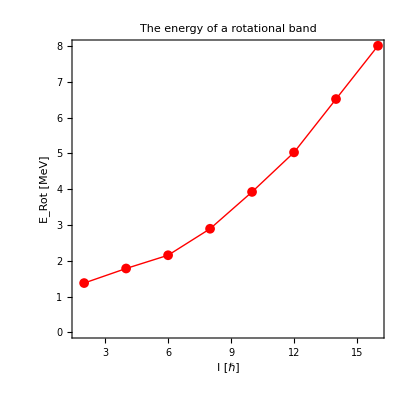

```mathematica
spins=Table[2i,{i,1,8,1}];
erot=Table[spins[[i]]*0.025(spins[[i]]+1)+RandomReal[{1,1.3}],{i,1,Length[spins]}];
dataExp=Table[{spins[[i]],erot[[i]]},{i,1,Length[erot]}];
ListPlot[dataExp,FrameLabel->{"I [ℏ]","E_Rot [MeV]"},Frame->True,Axes->False,AspectRatio->1,PlotRange->Full,FrameStyle->Directive[Black,Thick],LabelStyle->{17,FontFamily->"Menlo"},PlotStyle->{Red,Thick},Joined->True,PlotMarkers->{Automatic, Medium},PlotLabel->"The energy of a\nrotational band"]
```

```mathematica
e2 = erot[[1]]; 
e4 = erot[[2]]; 
thetaR[I_] := Values[Solve[x^3 - a*x^2 - (1/(2*c))*I*(I + 1) == 0, x][[1,1]]]; 
enR[I_,θ_,a_,c_]:=1/(2*θ)I(I+1)+1/2 c(θ-a)^2;
```

```mathematica
theta20=thetaR[2];
theta40=thetaR[4];
```

```mathematica
(*theta20
theta40*)
enR[2,theta20,a,c]
enR[4,theta40,a,c]
```

9/(a+(2^(1/3) a^2)/((2 a^3+81/c+(9 √(81+4 a^3 c))/c)^(1/3))+((2 a^3+81/c+(9 √(81+4 a^3 c))/c)^(1/3))/2^(1/3))+1/2 c (-a+1/3 (a+(2^(1/3) a^2)/((2 a^3+81/c+(9 √(81+4 a^3 c))/c)^(1/3))+((2 a^3+81/c+(9 √(81+4 a^3 c))/c)^(1/3))/2^(1/3)))^2

30/(a+a^2/((a^3+135/c+(3 √15 √(135+2 a^3 c))/c)^(1/3))+(a^3+135/c+(3 √15 √(135+2 a^3 c))/c)^(1/3))+1/2 c (-a+1/3 (a+a^2/((a^3+135/c+(3 √15 √(135+2 a^3 c))/c)^(1/3))+(a^3+135/c+(3 √15 √(135+2 a^3 c))/c)^(1/3)))^2

```mathematica
NSolve[{enR[2,theta20,a,c]==erot[[1]],enR[4,theta40,a,c]==erot[[2]]},{a,c}]
```

$Aborted